# Algoritmo ID3

Fuente: CSE5230 Tutorial: The ID3 Decision Tree Algoritm, MONASH UNIVERSITY

Descripción

ID3 es un algoritmo de aprendizaje de árbol de decisión. El aprendizaje por árbol de decisión es un método para aproximar una función de elementos discretos. Existen también otros algoritmos de aprendizaje basados en árbol de decisión como: C4.5, C5.0, CART, CHAID, de los cuales los dos primeros fueron concebidos como una mejora al ID3.

ID3 sigue el principio de la navaja de Ockham, buscando encontrar la mejor explicación para un conjunto de datos maximizando la ganancia de información. Para ello se usa una medida que en teoría de la información se denomina entropía. En este contexto la entropía es una medida acerca de la incertidumbre de la fuente del mensaje. Cuanto mayor sea la incertidumbre de un receptor de mensajes acerca de la fuente, mayor será la información que necesitará el receptor para saber que el mensaje ha sido enviado.

Implementación

Primero se carga una base de datos. Para este algoritmo se usarán bases de datos sin entradas faltantes. Se define como T a la base de datos y C el atributo que se desea predecir. En este ejemplo se desea predecir el atributo Resultado.

```mathematica
LoadDatabase[file_]:=Block[{rawData,rawDataKeys,rawDataAttributes,dataset},
rawData = Import[FileNameJoin[{NotebookDirectory[],file}]];
rawDataKeys = First[rawData];
rawDataAttributes = Rest[rawData];
dataset = Dataset[Map[Association[MapThread[#1->#2&,{rawDataKeys,#}]]&,rawDataAttributes]];
Return[{Keys[First[dataset]],dataset}];
];
```

```mathematica
{keys,dataset} = LoadDatabase["Medicamento.csv"];
```

```mathematica
dataset
```

Dataset[<>]

El número promedio de bits requeridos para identificar un mensaje es una medida de la incertidumbre de la fuente y a este se le conoce como entropía de la fuente.
Considere una fuente S que puede producir n mensajes (m_1, m_2, ..., m_n). Para la fuente S con una distribución de probabilidad de mensajes P = (p_1, p_2, ..., p_n), la entropía H(P) es

H(P) = -∑_(i=1)^n p_i log (p_i)

Un ejemplo de esto se muestra en la figura, en la cual se muestra la entropía asociada a un mensaje con probabilidad p_1 = p, y p_2 = 1-p. La entropía tiene un máximo cuando la aleatoriedad del ensaje es máxima, es decir cuando p_1 = p_2.

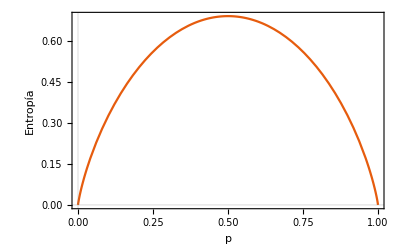

```mathematica
BinaryDistEntropy[p_]:=-p Log[p]-(1-p)Log[1-p];
Plot[BinaryDistEntropy[p],{p,0,1},PlotTheme->"Scientific",FrameLabel->{"p","Entropía"}]
```

Ahora, consideremos un conunto de datos T particionado en k clases {C_1, C_2, ..., C_k} de manera que

P(C_i) = (|C_i|)/(|T|)

y

H(T) = -∑_(i=1)^n P(C_i) log P(C_i)

Si se realiza una partición de T en base a un atributo de entrada X en subconjuntos T_1, T_2, ..., T_n, la información necesaria para identificar la clase de un elemento de T es el promedio ponderado de la información necesaria para identificar la clase de un elemento de cada subconjunto.

H(X,T) = -∑_(i=1)^n (|T_i|)/(|T|) H(T_i)

```mathematica
CalcEntropy[T_]:=Entropy[2,Normal[T]];
```

```mathematica
N[CalcEntropy[dataset[All,"Administrar"]]]
```

0.863121

Si se realiza una partición de T en base a un atributo de entrada X en subconjuntos T_1, T_2, ..., T_n, la información necesaria para identificar la clase de un elemento de T es el promedio ponderado de la información necesaria para identificar la clase de un elemento de cada subconjunto.

H(X,T) = -∑_(i=1)^n (|T_i|)/(|T|) H(T_i)

```mathematica
PartialEntropy[X_,T_,Cl_]:=Block[{grouped},
grouped = T[GroupBy[X]];
Total[Map[N[Count[T[All,X],#]/Length[T[All,X]]*CalcEntropy[grouped[#,All,Cl]]]&,Keys[grouped]]]
];
```

```mathematica
PartialEntropy["Presion",dataset,"Administrar"]
```

0.409188

Para construir nuestro árbol de decisión nos interesa saber cuánta información acerca del atributo de salida (Resultado) se puede obtener conociendo un atributo de entrada X. Se define esta ganancia de información como

G(X,T) = H(T) - H(X,T)

```mathematica
InformationGain[X_,T_,Cl_]:=Ramp[CalcEntropy[T[All,Cl]]-PartialEntropy[X,T,Cl]];
```

```mathematica
InformationGain["Presion",dataset,"Administrar"]
```

0.272788

El algoritmo ID3 calcula la ganancia de información para cada atributo X, y a partir del atributo que maximiza la ganancia de información crea un subconjunto de T agrupando cada posible valor de X.

```mathematica
AttributesInformationGain[XS_,T_,Cl_]:=Map[{#,InformationGain[#,T,Cl]}&,Normal[XS]];
```

```mathematica
Dataset[AttributesInformationGain[Drop[Normal[keys],-1],dataset,"Administrar"]]
```

Dataset[<>]

Y se vuelve a realizar el mismo procedimiento anterior haciendo particiones de T según los posibles valores de X.

```mathematica
dataset[GroupBy["Presion"]]
```

Dataset[<>]

```mathematica
{dataset[GroupBy["Presion"]]["Alta"],dataset[GroupBy["Presion"]]["Media"],dataset[GroupBy["Presion"]]["Baja"]}
```

{Dataset[<>],Dataset[<>],Dataset[<>]}

```mathematica
Map[N[CalcEntropy[#]]&,{dataset[GroupBy["Presion"]]["Alta"],dataset[GroupBy["Presion"]]["Media"],dataset[GroupBy["Presion"]]["Baja"]}]
```

{2.58496,1.58496,1.52193}

```mathematica
Map[Dataset[AttributesInformationGain[Drop[Normal[keys],-1],#,"Administrar"]]&,{dataset[GroupBy["Presion"]]["Alta"],dataset[GroupBy["Presion"]]["Media"],dataset[GroupBy["Presion"]]["Baja"]}]
```

{Dataset[<>],Dataset[<>],Dataset[<>]}

Algoritmo principal del ID3 se puede definir de forma recursiva, añadiendo Nodos por cada partición de T hasta que no se puede realizar particiones y la recursión termina.

```mathematica
ID3[X_,T_,Cl_]:=Block[{gains,subX,branches,branchResults},
(* Si la base de datos está vacía devuelve error *)
If[Length[T] == 0,
Return["Failure"]
];

(* Si la base de datos sólo contiene una clase a predecir, devuelve esa clase *)
If[CountDistinct[T[All,Cl]]== 1, 
Return[StringJoin[Cl,": ",First[DeleteDuplicates[T[All,Cl]]]]]
];

(* Calcula ganancia de cada atributo y escoge el atributo de mayor ganancia *)
gains = Dataset[AttributesInformationGain[X,T,Cl]];
subX = TakeLargestBy[gains,Last,1][1,1];
branches = T[GroupBy[subX]];

(* Si sólo hay un atributo, devuelve la clase más común *)
If[CountDistinct[Normal[Keys[branches]]]== 1, 
Return[StringJoin[Cl,": ",First[Commonest[T[All,Cl],1]]]]
];

(* Si todavía hay varios atributos en la base de datos, calcula ID3 con la base de datos reducida *)
branchResults = Map[
{subX,#,ID3[X,branches[#],Cl]}&,
Normal[Keys[branches]]
];
Return[branchResults];
];
MakeGraph[nestedList_]:=Block[{rule,vertex},
rule = {x_,label_String,rest__}:>
If[Length[rest]== 0,
Labeled[DirectedEdge[x,rest],label],
Map[{Labeled[DirectedEdge[x,First[#]],label],#}&,rest]
];
vertex = ReplaceRepeated[nestedList,rule];
Return[DeleteDuplicates[Flatten[vertex]]];
];
```

```mathematica
id3Nested = ID3[Drop[keys,-1],dataset,Last[keys]];
graphVertex = MakeGraph[id3Nested];
```

```mathematica
Graph[graphVertex,VertexLabels->Automatic,PlotLabel->"Administrar fármaco",PlotTheme->"Scientific"]
```

-Graphics-

Para realizar la validación se construye un árbol de switches basados en el resultado del algoritmo ID3

```mathematica
BranchSwitch[data_,tree_]:=Block[{switch,vertex,branches,subVertex},
If[Length[tree]>0,
vertex = First[tree[[All,1]]];
branches = tree[[All,2]];
subVertex = Map[BranchSwitch[data,#]&,tree[[All,3]]];

switch = Apply[Switch,Join[{data[vertex]},Flatten[Transpose[{branches,subVertex}],1]]];
Return[switch];
,
Return[tree];
];
];
ID3Prediction[data_,tree_,predict_]:=Block[{prediction,deleteStr},
prediction = BranchSwitch[data,tree];
deleteStr = StringJoin[predict,": "];
Return[StringDelete[prediction,deleteStr]];
];
SucessRateID3[dataset_,tree_,predict_]:=Block[{dataPredict,modelPredict,matches},
dataPredict = Normal[dataset[All,predict]];
modelPredict = Normal[Map[ID3Prediction[#,tree,predict]&,dataset]];
matches = Count[MapThread[SameQ,{dataPredict,modelPredict}],True];
Return[100*matches/Length[dataPredict]];
];
```

```mathematica
Map[Append[#,"Prediccion"->ID3Prediction[#,id3Nested,"Administrar"]]&,dataset]
```

Dataset[<>]

```mathematica
SucessRateID3[dataset,id3Nested,"Administrar"]
```

100

## Información detallada

Algoritmo ID3 con panel de entropías y base de datos T en cada paso.

```mathematica
ID3Labeled[X_,T_,Cl_]:=Block[{gains,subX,branches,branchResults},
If[Length[T] == 0,
Return["Failure"]
];

If[CountDistinct[T[All,Cl]]== 1, 
Return[StringJoin[Cl,": ",First[DeleteDuplicates[T[All,Cl]]]]];
];

gains = Dataset[AttributesInformationGain[X,T,Cl]];
subX = TakeLargestBy[gains,Last,1][1,1];
branches = T[GroupBy[subX]];

If[CountDistinct[Normal[Keys[branches]]]== 1, 
Return[StringJoin[Cl,": ",First[Commonest[T[All,Cl],1]]]];
];

branchResults = Map[
{TabView[{"Entropias"->Labeled[gains,subX,Top],"Datos"->T},ImageSize->Automatic],#,ID3Labeled[X,branches[#],Cl]}&,
Normal[Keys[branches]]
];
Return[branchResults];
];
```

```mathematica
id3Nested = ID3Labeled[Drop[keys,-1],dataset,Last[keys]];
graphVertex = MakeGraph[id3Nested];
```

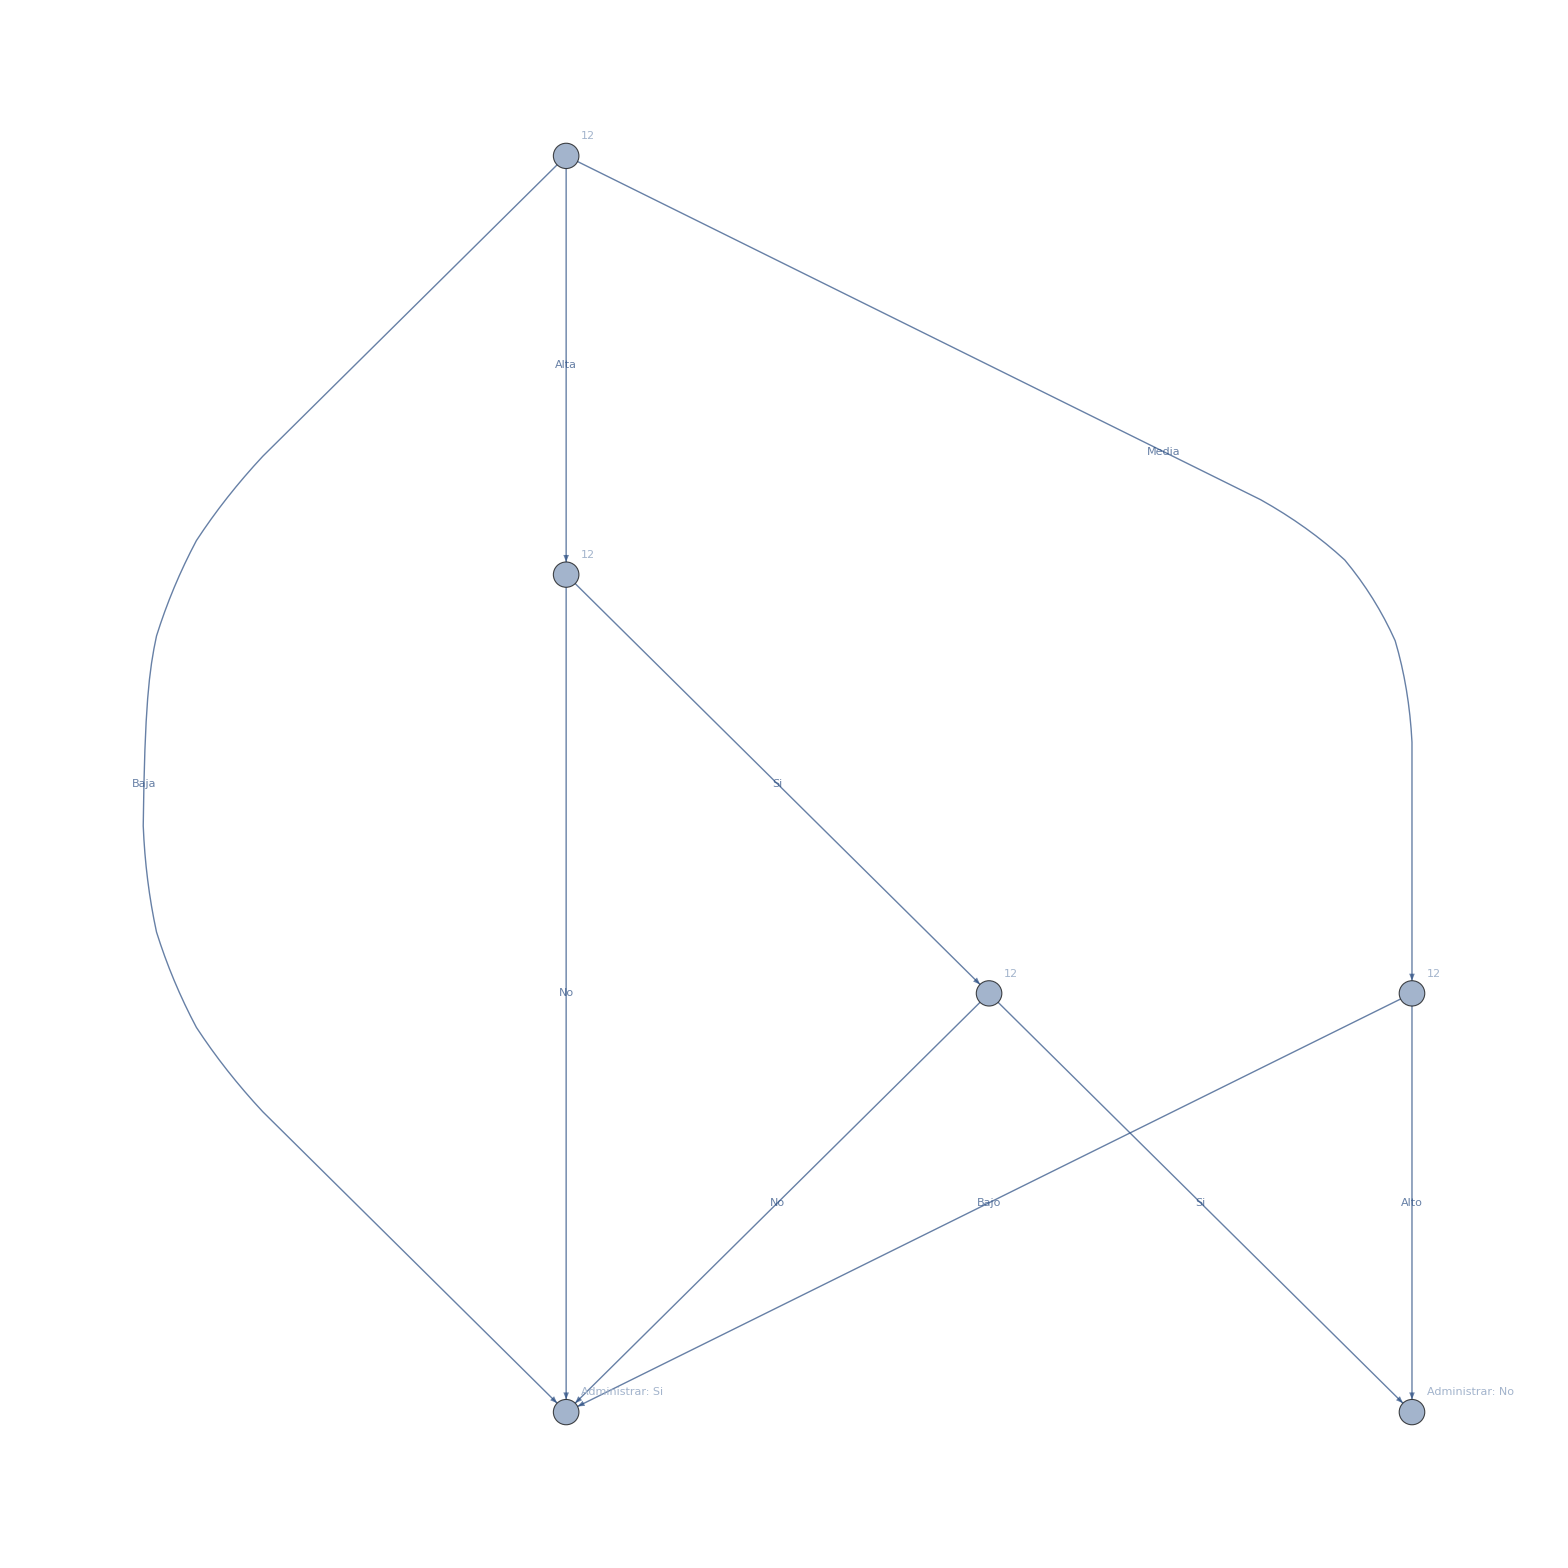

```mathematica
Graph[graphVertex,ImageSize->1600,VertexLabels->Automatic]
```

## Termografía

Base de datos médica de diagnósticos a partir de una termografía

```mathematica
{keys,dataset} = LoadDatabase["Termografia.csv"];
```

```mathematica
dataset
```

Vista simple

```mathematica
id3Nested = ID3[Drop[keys,-1],dataset,Last[keys]];
```

```mathematica
graphVertex = MakeGraph[id3Nested];
Graph[graphVertex,VertexLabels->Automatic,PlotTheme->"Scientific"]
```

Vista detallada

```mathematica
ID3Labeled[X_,T_,Cl_]:=Block[{gains,subX,branches,branchResults},
If[Length[T] == 0,
Return["Failure"]
];

If[CountDistinct[T[All,Cl]]== 1, 
Return[StringJoin[Cl,": ",First[DeleteDuplicates[T[All,Cl]]]]];
];

gains = Dataset[AttributesInformationGain[X,T,Cl]];
subX = TakeLargestBy[gains,Last,1][1,1];
branches = T[GroupBy[subX]];

If[CountDistinct[Normal[Keys[branches]]]== 1, 
Return[StringJoin[Cl,": ",First[Commonest[T[All,Cl],1]]]];
];

branchResults = Map[
{Row[{Labeled[Labeled[gains,subX,Top],Style["Entropias",Bold],Top],Labeled[T,Style["Datos",Bold],Top]},ImageSize->Automatic],#,ID3Labeled[X,branches[#],Cl]}&,
Normal[Keys[branches]]
];
Return[branchResults];
];
id3Nested = ID3Labeled[Drop[keys,-1],dataset,Last[keys]];
graphVertex = MakeGraph[id3Nested];
Graph[graphVertex,ImageSize->1600,VertexLabels->Placed["Name",Tooltip]]
```

Validación

```mathematica
id3Nested = ID3[Drop[keys,-1],dataset,Last[keys]];
Map[Append[#,"Prediccion"->ID3Prediction[#,id3Nested,"CLASE "]]&,dataset]
```

```mathematica
N[SucessRateID3[dataset,id3Nested,"CLASE "]]
```